```mathematica
(* Jack Farrell, Dept. of Physics, University of Toronto, 2020 *)
(* Investigating the frequency and growth rate of the quasinormal modes of the Dyakonov-Shur Instability of viscous electrons in an annular geometry *)

ClearAll[v0,η,γ,ratio,R1,R2,eq1,eq2,u,n,rawVals, num, list];
SetDirectory[NotebookDirectory[]];
etas = Table[i,{i,0.0000,0.15,0.003}];
v0s = Table[i,{i,0.0000,0.25,0.005}]
freqs=Table[0,{i,1,Length[v0s]}];
rates=Table[0,{i,1,Length[v0s]}];
num=1
list = Table[{},{i, 1, Length[v0s]^2}];
For[i=1,i<Length[v0s]+1,i++,
For[j=1,j<Length[v0s]+1,j++,
v0=v0s[[i]];
η=etas[[j]];
γ=0.1;

ratio = 0.001;
R1 = 1/ratio;
R2 = R1+1;

eq1 = D[u[t,r],t] + v0^2*R2^2/r*n[t,r]+2*v0*R2*D[u[t,r]/r,r]+r*D[n[t,r],r] - r*η*(D[u[t,r]/r,{r,2}]+1/r*D[u[t,r]/r, r])==-γ*u[t,r]+γ *n[t,r]*v0*R2 +NeumannValue[0,r==R1];
eq2 = D[n[t,r],t]+1/r*D[u[t,r],r]==0;

rawVals=NDEigenvalues[{eq1,eq2,DirichletCondition[u[t,r]==0,r==R2],DirichletCondition[n[t,r]==0,r==R1]},{u[t,r],n[t,r]},t,{r,R1,R2},10];
vals=Sort[I*rawVals,Abs[Re[#1]-Pi/2]<Abs[Re[#2]-Pi/2]&];
val=vals[[1]];
If[Im[val]>=0,
list[[num]]={v0, η, Re[val]};,
list[[num]]={v0, η, Empty}];
num = num + 1;
]]
```

{0.,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25}

1

```mathematica
list
```

{{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.0125,eta,Empty},{0.025,eta,1.35979},{0.025,eta,1.36268},{0.025,eta,1.36093},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.025,eta,Empty},{0.0375,eta,1.35882},{0.0375,eta,1.36183},{0.0375,eta,1.36027},{0.0375,eta,1.35957},{0.0375,eta,1.35964},{0.0375,eta,1.36004},{0.0375,eta,1.3605},{0.0375,eta,1.3609},{0.0375,eta,1.36122},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.0375,eta,Empty},{0.05,eta,1.35722},{0.05,eta,1.36035},{0.05,eta,1.35898},{0.05,eta,1.3584},{0.05,eta,1.35856},{0.05,eta,1.35904},{0.05,eta,1.35959},{0.05,eta,1.36009},{0.05,eta,1.36051},{0.05,eta,1.36085},{0.05,eta,1.36113},{0.05,eta,1.36135},{0.05,eta,1.36154},{0.05,eta,1.36169},{0.05,eta,1.36183},{0.05,eta,1.36194},{0.05,eta,Empty},{0.05,eta,Empty},{0.05,eta,Empty},{0.05,eta,Empty},{0.05,eta,Empty},{0.0625,eta,1.355},{0.0625,eta,1.35825},{0.0625,eta,1.35706},{0.0625,eta,1.35661},{0.0625,eta,1.35687},{0.0625,eta,1.35743},{0.0625,eta,1.35806},{0.0625,eta,1.35865},{0.0625,eta,1.35917},{0.0625,eta,1.35962},{0.0625,eta,1.36001},{0.0625,eta,1.36035},{0.0625,eta,1.36065},{0.0625,eta,1.36091},{0.0625,eta,1.36116},{0.0625,eta,1.36138},{0.0625,eta,1.36158},{0.0625,eta,1.36176},{0.0625,eta,1.36193},{0.0625,eta,1.36208},{0.0625,eta,1.36222},{0.075,eta,1.35216},{0.075,eta,1.35553},{0.075,eta,1.35451},{0.075,eta,1.3542},{0.075,eta,1.35455},{0.075,eta,1.3552},{0.075,eta,1.35592},{0.075,eta,1.3566},{0.075,eta,1.35723},{0.075,eta,1.35778},{0.075,eta,1.35828},{0.075,eta,1.35873},{0.075,eta,1.35914},{0.075,eta,1.35952},{0.075,eta,1.35987},{0.075,eta,1.36021},{0.075,eta,1.36052},{0.075,eta,1.36081},{0.075,eta,1.36109},{0.075,eta,1.36135},{0.075,eta,1.36159},{0.0875,eta,1.34871},{0.0875,eta,1.3522},{0.0875,eta,1.35135},{0.0875,eta,1.35116},{0.0875,eta,1.35161},{0.0875,eta,1.35235},{0.0875,eta,1.35316},{0.0875,eta,1.35395},{0.0875,eta,1.35467},{0.0875,eta,1.35534},{0.0875,eta,1.35594},{0.0875,eta,1.3565},{0.0875,eta,1.35703},{0.0875,eta,1.35752},{0.0875,eta,1.35798},{0.0875,eta,1.35843},{0.0875,eta,1.35885},{0.0875,eta,1.35926},{0.0875,eta,1.35964},{0.0875,eta,1.36001},{0.0875,eta,1.36037},{0.1,eta,1.34464},{0.1,eta,1.34825},{0.1,eta,1.34758},{0.1,eta,1.34752},{0.1,eta,1.34806},{0.1,eta,1.34889},{0.1,eta,1.3498},{0.1,eta,1.35068},{0.1,eta,1.35152},{0.1,eta,1.35229},{0.1,eta,1.35301},{0.1,eta,1.35368},{0.1,eta,1.35431},{0.1,eta,1.35492},{0.1,eta,1.3555},{0.1,eta,1.35605},{0.1,eta,1.35659},{0.1,eta,1.3571},{0.1,eta,1.3576},{0.1,eta,1.35808},{0.1,eta,1.35855},{0.1125,eta,1.33997},{0.1125,eta,1.34369},{0.1125,eta,1.34319},{0.1125,eta,1.34326},{0.1125,eta,1.34391},{0.1125,eta,1.34483},{0.1125,eta,1.34584},{0.1125,eta,1.34682},{0.1125,eta,1.34776},{0.1125,eta,1.34864},{0.1125,eta,1.34947},{0.1125,eta,1.35026},{0.1125,eta,1.35101},{0.1125,eta,1.35172},{0.1125,eta,1.35242},{0.1125,eta,1.35309},{0.1125,eta,1.35373},{0.1125,eta,1.35436},{0.1125,eta,1.35497},{0.1125,eta,1.35556},{0.1125,eta,1.35614},{0.125,eta,1.33469},{0.125,eta,1.33854},{0.125,eta,1.3382},{0.125,eta,1.3384},{0.125,eta,1.33916},{0.125,eta,1.34018},{0.125,eta,1.34128},{0.125,eta,1.34237},{0.125,eta,1.34341},{0.125,eta,1.3444},{0.125,eta,1.34535},{0.125,eta,1.34625},{0.125,eta,1.34711},{0.125,eta,1.34794},{0.125,eta,1.34875},{0.125,eta,1.34953},{0.125,eta,1.35029},{0.125,eta,1.35103},{0.125,eta,1.35176},{0.125,eta,1.35246},{0.125,eta,1.35315},{0.1375,eta,1.32881},{0.1375,eta,1.33278},{0.1375,eta,1.33261},{0.1375,eta,1.33294},{0.1375,eta,1.33381},{0.1375,eta,1.33493},{0.1375,eta,1.33613},{0.1375,eta,1.33733},{0.1375,eta,1.33848},{0.1375,eta,1.33958},{0.1375,eta,1.34064},{0.1375,eta,1.34165},{0.1375,eta,1.34263},{0.1375,eta,1.34358},{0.1375,eta,1.3445},{0.1375,eta,1.3454},{0.1375,eta,1.34628},{0.1375,eta,1.34713},{0.1375,eta,1.34797},{0.1375,eta,1.34878},{0.1375,eta,1.34958},{0.15,eta,1.32234},{0.15,eta,1.32644},{0.15,eta,1.32643},{0.15,eta,1.32689},{0.15,eta,1.32787},{0.15,eta,1.32909},{0.15,eta,1.3304},{0.15,eta,1.3317},{0.15,eta,1.33297},{0.15,eta,1.33418},{0.15,eta,1.33535},{0.15,eta,1.33649},{0.15,eta,1.33758},{0.15,eta,1.33865},{0.15,eta,1.33968},{0.15,eta,1.3407},{0.15,eta,1.34169},{0.15,eta,1.34266},{0.15,eta,1.34361},{0.15,eta,1.34454},{0.15,eta,1.34545},{0.1625,eta,1.31528},{0.1625,eta,1.31951},{0.1625,eta,1.31966},{0.1625,eta,1.32026},{0.1625,eta,1.32135},{0.1625,eta,1.32268},{0.1625,eta,1.32409},{0.1625,eta,1.3255},{0.1625,eta,1.32688},{0.1625,eta,1.32821},{0.1625,eta,1.3295},{0.1625,eta,1.33075},{0.1625,eta,1.33196},{0.1625,eta,1.33314},{0.1625,eta,1.3343},{0.1625,eta,1.33543},{0.1625,eta,1.33654},{0.1625,eta,1.33762},{0.1625,eta,1.33869},{0.1625,eta,1.33973},{0.1625,eta,1.34076},{0.175,eta,1.30765},{0.175,eta,1.31199},{0.175,eta,1.31232},{0.175,eta,1.31305},{0.175,eta,1.31425},{0.175,eta,1.31569},{0.175,eta,1.31721},{0.175,eta,1.31873},{0.175,eta,1.32022},{0.175,eta,1.32167},{0.175,eta,1.32308},{0.175,eta,1.32444},{0.175,eta,1.32578},{0.175,eta,1.32708},{0.175,eta,1.32835},{0.175,eta,1.3296},{0.175,eta,1.33083},{0.175,eta,1.33203},{0.175,eta,1.33321},{0.175,eta,1.33437},{0.175,eta,1.33552},{0.1875,eta,1.29943},{0.1875,eta,1.30391},{0.1875,eta,1.30439},{0.1875,eta,1.30526},{0.1875,eta,1.30658},{0.1875,eta,1.30813},{0.1875,eta,1.30976},{0.1875,eta,1.3114},{0.1875,eta,1.31301},{0.1875,eta,1.31457},{0.1875,eta,1.3161},{0.1875,eta,1.31758},{0.1875,eta,1.31904},{0.1875,eta,1.32046},{0.1875,eta,1.32185},{0.1875,eta,1.32322},{0.1875,eta,1.32456},{0.1875,eta,1.32589},{0.1875,eta,1.32719},{0.1875,eta,1.32847},{0.1875,eta,1.32973},{0.2,eta,1.29065},{0.2,eta,1.29526},{0.2,eta,1.2959},{0.2,eta,1.2969},{0.2,eta,1.29835},{0.2,eta,1.30001},{0.2,eta,1.30176},{0.2,eta,1.30351},{0.2,eta,1.30523},{0.2,eta,1.30692},{0.2,eta,1.30856},{0.2,eta,1.31017},{0.2,eta,1.31174},{0.2,eta,1.31329},{0.2,eta,1.3148},{0.2,eta,1.31629},{0.2,eta,1.31776},{0.2,eta,1.3192},{0.2,eta,1.32062},{0.2,eta,1.32202},{0.2,eta,1.32339},{0.2125,eta,1.2813},{0.2125,eta,1.28604},{0.2125,eta,1.28685},{0.2125,eta,1.28799},{0.2125,eta,1.28955},{0.2125,eta,1.29133},{0.2125,eta,1.29319},{0.2125,eta,1.29506},{0.2125,eta,1.29691},{0.2125,eta,1.29871},{0.2125,eta,1.30048},{0.2125,eta,1.30221},{0.2125,eta,1.30391},{0.2125,eta,1.30557},{0.2125,eta,1.30721},{0.2125,eta,1.30882},{0.2125,eta,1.31041},{0.2125,eta,1.31197},{0.2125,eta,1.31351},{0.2125,eta,1.31503},{0.2125,eta,1.31652},{0.225,eta,1.27139},{0.225,eta,1.27627},{0.225,eta,1.27723},{0.225,eta,1.27851},{0.225,eta,1.2802},{0.225,eta,1.2821},{0.225,eta,1.28408},{0.225,eta,1.28607},{0.225,eta,1.28803},{0.225,eta,1.28996},{0.225,eta,1.29185},{0.225,eta,1.29371},{0.225,eta,1.29553},{0.225,eta,1.29732},{0.225,eta,1.29908},{0.225,eta,1.30081},{0.225,eta,1.30252},{0.225,eta,1.30421},{0.225,eta,1.30587},{0.225,eta,1.30751},{0.225,eta,1.30912},{0.2375,eta,1.26093},{0.2375,eta,1.26594},{0.2375,eta,1.26706},{0.2375,eta,1.26849},{0.2375,eta,1.2703},{0.2375,eta,1.27232},{0.2375,eta,1.27442},{0.2375,eta,1.27653},{0.2375,eta,1.27862},{0.2375,eta,1.28067},{0.2375,eta,1.28269},{0.2375,eta,1.28467},{0.2375,eta,1.28661},{0.2375,eta,1.28853},{0.2375,eta,1.29041},{0.2375,eta,1.29227},{0.2375,eta,1.2941},{0.2375,eta,1.29591},{0.2375,eta,1.29769},{0.2375,eta,1.29946},{0.2375,eta,1.30119},{0.25,eta,1.24992},{0.25,eta,1.25506},{0.25,eta,1.25635},{0.25,eta,1.25791},{0.25,eta,1.25985},{0.25,eta,1.262},{0.25,eta,1.26422},{0.25,eta,1.26645},{0.25,eta,1.26866},{0.25,eta,1.27084},{0.25,eta,1.27299},{0.25,eta,1.27509},{0.25,eta,1.27716},{0.25,eta,1.27921},{0.25,eta,1.28122},{0.25,eta,1.2832},{0.25,eta,1.28516},{0.25,eta,1.28709},{0.25,eta,1.289},{0.25,eta,1.29088},{0.25,eta,1.29274}}

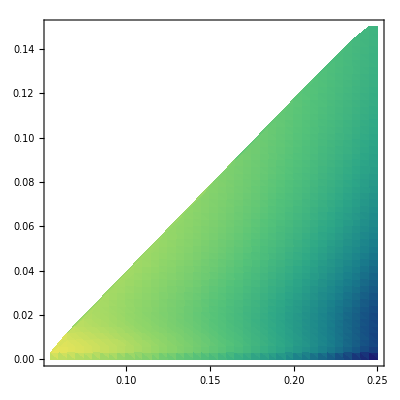

```mathematica
ListDensityPlot[list,ColorFunction->"BlueGreenYellow", InterpolationOrder->1]
```